```mathematica
c = 1; b = 1; m = 1; p = 1; g = 1;
SEIR = NDSolve[{s'[t]==c -b*s[t]*i[t] -m*s[t],e'[t] == b * s[t] * i[t] - (p + m) * e[t],i'[t] == p * e[t] - (g + m) * i[t],r'[t] == g * i[t] - m * r[t],s[0]==1000,e[0]==1,i[0]== r[0]==0},{s[t],e[t],i[t], r[t]},{t,0,10},MaxSteps->100]
```

{{s[t]→InterpolatingFunction[{{0., 10.}}, <>][t],e[t]→InterpolatingFunction[{{0., 10.}}, <>][t],i[t]→InterpolatingFunction[{{0., 10.}}, <>][t],r[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

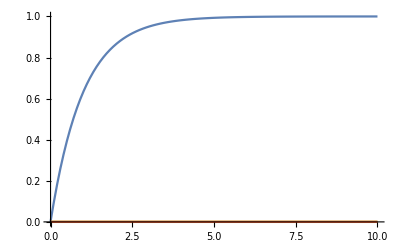

```mathematica
Plot[Evaluate[{s[t],e[t],i[t], r[t]} /. SEIR], {t,0,10}, PlotRange -> All, PlotPoints-> 100]
```